```mathematica
D[Exp[f[x]x]]==1
```

ⅇ^(x f[x])==1

```mathematica
Solve[ⅇ^(x f[x])==1,f[x]]
```

{{f[x]→ConditionalExpression[(2 ⅈ π C[1])/x,C[1]∈ℤ]}}

```mathematica
ConditionalExpression[D[Exp[(2 ⅈ π C[1])/x],x],C[1]∈Integers]
```

ConditionalExpression[-(2 ⅈ ⅇ^((2 ⅈ π C[1])/x) π C[1])/x^2,C[1]∈ℤ]

```mathematica
Exp[(2 ⅈ π)/x]
```

ⅇ^((2 ⅈ π)/x)

```mathematica
D[Exp[f[x]x]]/Exp[f[x]]==1
```

ⅇ^(-f[x]+x f[x])==1

```mathematica
Solve[ⅇ^(-f[x]+x f[x])==1,f[x]]
```

{{f[x]→ConditionalExpression[(2 ⅈ π C[1])/(-1+x),C[1]∈ℤ]}}

```mathematica
D[Exp[(2 ⅈ π C[1])/(-1+x)],x]/Exp[(2 ⅈ π C[1])/(-1+x)]
```

-(2 ⅈ π C[1])/(-1+x)^2

```mathematica
D[Exp[f[x]],x]/Exp[f[x]]==1
```

f'[x]==1

```mathematica
DSolve[f'[x]==1,{f[x]},{x}]
```

{{f[x]→x+C[1]}}

```mathematica
Dt[f[x]]/f[x]==1
```

(Dt[x] f'[x])/f[x]==1

```mathematica
Solve[(Dt[x] f'[x])/f[x]==1,f[x]]
```

{{f[x]→Dt[x] f'[x]}}

```mathematica
{a,b}.{c,d}
```

a c+b d

```mathematica
f[{1,1}.{c,d}]=={1,1}
```

f[c+d]=={1,1}

```mathematica
f[{a,b}.{c,d}]=={a,b}
```

f[a c+b d]=={a,b}

```mathematica
Dt[f[x]g[x]]
```

Dt[x] g[x] f'[x]+Dt[x] f[x] g'[x]

```mathematica
{Dt[x],Dt[x]} {1,2}
```

{Dt[x],2 Dt[x]}

```mathematica
{Dt[x],Dt[x]} {{1,1},{2,2}}
```

{{Dt[x],Dt[x]},{2 Dt[x],2 Dt[x]}}

```mathematica
{Dt[x],Dt[x]} ({f[x],g[x]} {f'[x],g'[x]})
```

{Dt[x] f[x] f'[x],Dt[x] g[x] g'[x]}

```mathematica
Dt[x] ({f[x],g[x]} {f'[x],g'[x]})
```

{Dt[x] f[x] f'[x],Dt[x] g[x] g'[x]}

```mathematica
Dt[x] ({f[x],g[x]}.{f'[x],g'[x]})
```

Dt[x] (f[x] f'[x]+g[x] g'[x])

```mathematica
Dt[x] ({f[x],g[x]}.{g'[x],f'[x]})
```

Dt[x] (g[x] f'[x]+f[x] g'[x])

```mathematica
TraditionalForm@Inactivate[Dt[x] ({f[x],g[x]}.{g'[x],f'[x]})]
```

Dt[x]*{f[x],g[x]}.{Derivative[1][g][x],Derivative[1][f][x]}

```mathematica
Derivative[1][g][x]
```

g'[x]

```mathematica
TraditionalForm[Dt[x] (g[x] f'[x]+f[x] g'[x])]
```

ⅆx (g(x) f'(x)+f(x) g'(x))

```mathematica
ExpandAll[Dt[x] (g[x] f'[x]+f[x] g'[x])]
```

Dt[x] g[x] f'[x]+Dt[x] f[x] g'[x]

```mathematica
Sin[x]
```

Sin[x]

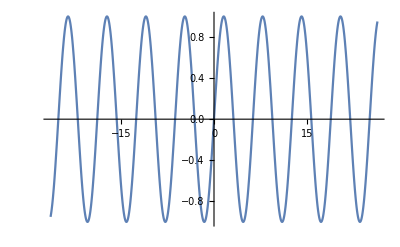

```mathematica
Plot[Sin[x],{x,-26.389378290154262,26.389378290154262}]
```

```mathematica
Sin'[0]
```

1

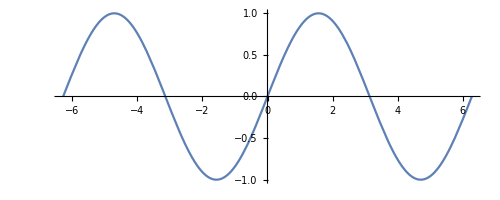

```mathematica
ParametricPlot[
{t,Sin[t]}
,{t,-2π,2π}]
```

```mathematica
Sin'[t]
```

Cos[t]

```mathematica
D[{t,Sin[t]},t]
```

{1,Cos[t]}

```mathematica
Manipulate[
ParametricPlot[
{t,Sin[t]}+α{1,Cos[t]}
,{t,-2π,2π}]
,{α,0,1}]
```

```mathematica
FullSimplify[Normalize@{1,Cos[t]},t∈Reals]
```

{1/(√(1+Cos[t]^2)),Cos[t]/(√(1+Cos[t]^2))}

```mathematica
Manipulate[
ParametricPlot[
{t,Sin[t]}+{1/(√(1+Cos[t]^2)),Cos[t]/(√(1+Cos[t]^2))}
,{t,-2π,2π}]
,{α,0,1}]
```

```mathematica
Sin[Subscript[t, 0]+α]==Sin[Subscript[t, 1]]
```

Sin[α+t_0]==Sin[t_1]

```mathematica
Solve[1==∫_0^a √(1+Sin'[t])ⅆt,a,Reals]
```

{}

```mathematica
1==∫_0^a √(1+Sin'[t])ⅆt
```

ConditionalExpression[1==-4 √2+2 √(1+Cos[a]) Tan[a/2],C[1]∈ℤ&&a+π<0&&a+π≤4 π C[1]&&C[1]≤0]

```mathematica
1==∫_0^a √(1+Sin'[t]^2)ⅆt
```

ConditionalExpression[1==√2 (EllipticE[π FractionalPart[a/π],1/2]+2 EllipticE[1/2] IntegerPart[a/π]),a∈ℝ]

```mathematica
1==√2 (EllipticE[π FractionalPart[a/π],1/2]+2 EllipticE[1/2] IntegerPart[a/π])/.a->1
```

False

```mathematica
FindInstance@ConditionalExpression[1==√2 (EllipticE[π FractionalPart[a/π],1/2]+2 EllipticE[1/2] IntegerPart[a/π]),a∈Reals]
```

FindInstance::argbu: FindInstance called with 1 argument; between 2 and 4 arguments are expected.

FindInstance[ConditionalExpression[1==√2 (EllipticE[π FractionalPart[a/π],1/2]+2 EllipticE[1/2] IntegerPart[a/π]),a∈ℝ]]

```mathematica
FindInstance[
ConditionalExpression[1==√2 (EllipticE[π FractionalPart[a/π],1/2]+2 EllipticE[1/2] IntegerPart[a/π]),a∈Reals]
,a]
```

FindInstance::nsmet: The methods available to FindInstance are insufficient to find the requested instances or prove they do not exist.

FindInstance[ConditionalExpression[1==√2 (EllipticE[π FractionalPart[a/π],1/2]+2 EllipticE[1/2] IntegerPart[a/π]),a∈ℝ],a]

```mathematica
FullSimplify[1==∫_0^a √(1+Sin'[t]^2)ⅆt,a∈]
```

√2 (EllipticE[π FractionalPart[a/π],1/2]+2 EllipticE[1/2] IntegerPart[a/π])==1

```mathematica
PositiveReals
```

```mathematica
Solve[√2 (EllipticE[π FractionalPart[a/π],1/2]+2 EllipticE[1/2] IntegerPart[a/π])==1,a,Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[√2 (EllipticE[π FractionalPart[a/π],1/2]+2 EllipticE[1/2] IntegerPart[a/π])==1,a,ℝ]

```mathematica
TraditionalForm[√2 (EllipticE[π FractionalPart[a/π],1/2]+2 EllipticE[1/2] IntegerPart[a/π])==1]
```

√2 (2 1/2 IntegerPart[a/π]+π frac(a/π)1/2)==1

```mathematica
Manipulate[
NIntegrate[√(1+Sin'[x]),{x,0,a}],{a,.0001,1}]
```

```mathematica
f[x]+ϵ η[x]
```

f[x]+ϵ η[x]